```mathematica
pt[n_]:=Table[Binomial[n,r],{r,0,n}]
```

```mathematica
Manipulate[DiscretePlot[Length@Select[pt[n],Not@Divisible[#,7]&],{n,1,7^p-1}],{p,1,3,1}]
```

```mathematica
Position[Table[Length@Select[pt[n],Not@Divisible[#,7]&],{n,0,1000}],0]
```

{}

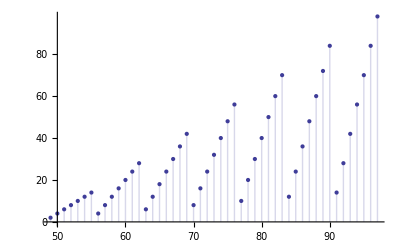

```mathematica
DiscretePlot[Length@Select[pt[n],Not@Divisible[#,7]&],{n,49,97}]
```

```mathematica
Table[Length@Select[pt[n],Not@Divisible[#,7]&],{n,0,250}]
```

{1,2,3,4,5,6,7,2,4,6,8,10,12,14,3,6,9,12,15,18,21,4,8,12,16,20,24,28,5,10,15,20,25,30,35,6,12,18,24,30,36,42,7,14,21,28,35,42,49,2,4,6,8,10,12,14,4,8,12,16,20,24,28,6,12,18,24,30,36,42,8,16,24,32,40,48,56,10,20,30,40,50,60,70,12,24,36,48,60,72,84,14,28,42,56,70,84,98,3,6,9,12,15,18,21,6,12,18,24,30,36,42,9,18,27,36,45,54,63,12,24,36,48,60,72,84,15,30,45,60,75,90,105,18,36,54,72,90,108,126,21,42,63,84,105,126,147,4,8,12,16,20,24,28,8,16,24,32,40,48,56,12,24,36,48,60,72,84,16,32,48,64,80,96,112,20,40,60,80,100,120,140,24,48,72,96,120,144,168,28,56,84,112,140,168,196,5,10,15,20,25,30,35,10,20,30,40,50,60,70,15,30,45,60,75,90,105,20,40,60,80,100,120,140,25,50,75,100,125,150,175,30,60,90,120,150,180,210,35,70,105,140,175,210,245,6,12,18,24,30,36}

```mathematica
Sum[Length@Select[pt[n],Not@Divisible[#,7]&],{n,0,7^3-1}]
```

21952

```mathematica
Log[7,10^9]//N
```

10.6497

```mathematica
10^9-3*7^10-3*7^9-5*7^8-3*7^7-1*7^6-6*7^5
```

307